## Extended Dicke model (two-atomic case)

```mathematica
bTb[λ_]:=DiagonalMatrix[{λ+1,λ,λ,λ-1}]
Sz:=DiagonalMatrix[{-1,0,0,1}]
DipDip:=Normal[SparseArray[{{2,3}->1,{3,2}->1},{4,4}]]
DipF[λ_]:={{0,√(λ+1),√(λ+1),0},{√(λ+1),0,0,√λ},
{√(λ+1),0,0,√λ},{0,√λ,√λ,0}}
H[ω_,ϵ_,V_,g_,λ_]:=ω bTb[λ]+ϵ Sz+V DipF[λ]+g DipDip
```

```mathematica
H
```

{{-ϵ+(1+λ) ω,V √(1+λ),V √(1+λ),0},{V √(1+λ),λ ω,g,V √λ},{V √(1+λ),g,λ ω,V √λ},{0,V √λ,V √λ,ϵ+(-1+λ) ω}}

```mathematica
Eigenvalues[H]
```

{-g+λ ω,Root[2 V^2 ϵ+g ϵ^2-2 V^2 ω-2 g ϵ ω+2 V^2 λ ω+ϵ^2 λ ω+4 V^2 λ^2 ω+g ω^2-2 ϵ λ ω^2-g λ^2 ω^2+λ ω^3-λ^3 ω^3+(-2 V^2-ϵ^2-4 V^2 λ+2 ϵ ω+2 g λ ω-ω^2+3 λ^2 ω^2) #1+(-g-3 λ ω) #1^2+#1^3&,1],Root[2 V^2 ϵ+g ϵ^2-2 V^2 ω-2 g ϵ ω+2 V^2 λ ω+ϵ^2 λ ω+4 V^2 λ^2 ω+g ω^2-2 ϵ λ ω^2-g λ^2 ω^2+λ ω^3-λ^3 ω^3+(-2 V^2-ϵ^2-4 V^2 λ+2 ϵ ω+2 g λ ω-ω^2+3 λ^2 ω^2) #1+(-g-3 λ ω) #1^2+#1^3&,2],Root[2 V^2 ϵ+g ϵ^2-2 V^2 ω-2 g ϵ ω+2 V^2 λ ω+ϵ^2 λ ω+4 V^2 λ^2 ω+g ω^2-2 ϵ λ ω^2-g λ^2 ω^2+λ ω^3-λ^3 ω^3+(-2 V^2-ϵ^2-4 V^2 λ+2 ϵ ω+2 g λ ω-ω^2+3 λ^2 ω^2) #1+(-g-3 λ ω) #1^2+#1^3&,3]}

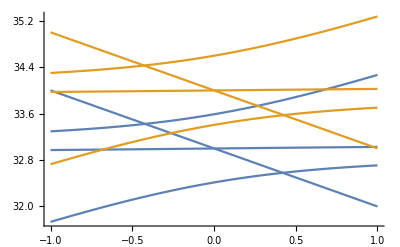

```mathematica
ω:=1
ϵ:=0.9
V:=0.05
Plot[{Eigenvalues[H[ω,ϵ,V,g,33]],Eigenvalues[H[ω,ϵ,V,g,34]]},{g,-1,1}]
```

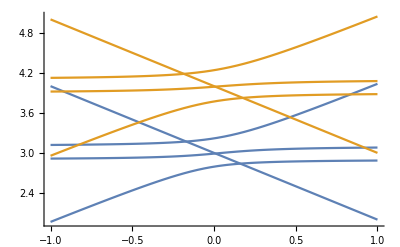

```mathematica
Plot[{Eigenvalues[H[ω,ϵ,V,g,3]],Eigenvalues[H[ω,ϵ,V,g,4]]},{g,-1,1}]
```

N.B. the states are _not_ degenerated at exactly g=0:

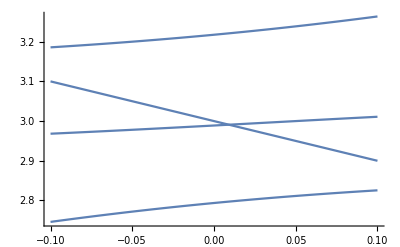

```mathematica
ω:=1
ϵ:=0.9
V:=0.05
Plot[{Eigenvalues[H[ω,ϵ,V,g,3]]},{g,-0.1,0.1}]
```

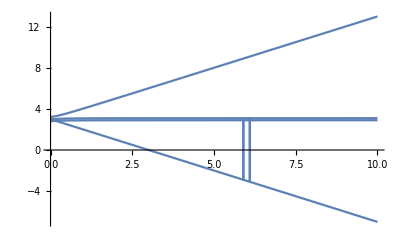

```mathematica
Plot[Eigenvalues[H[ω,ϵ,V,g,3]],{g,0,10}]
```

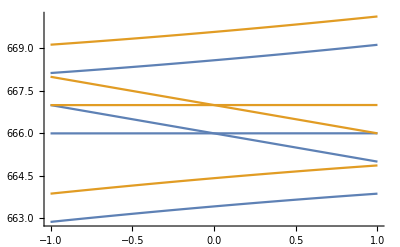

```mathematica
Plot[{Eigenvalues[H[ω,ϵ,V,g,666]],Eigenvalues[H[ω,ϵ,V,g,667]]},{g,-1,1}]
```

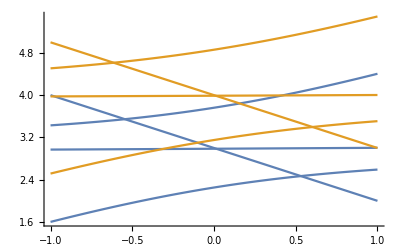

```mathematica
ω:=1
ϵ:=0.9
V:=0.2
Plot[{Eigenvalues[H[ω,ϵ,V,g,3]],Eigenvalues[H[ω,ϵ,V,g,4]]},{g,-1,1}]
```

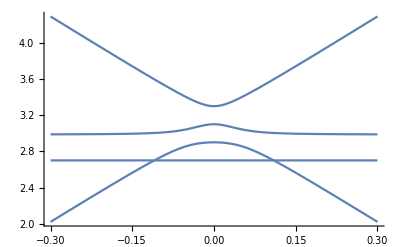

```mathematica
ω:=1
ϵ:=0.9
g:=0.3
Plot[Eigenvalues[H[ω,ϵ,V,g,3]],{V,-0.3,0.3}]
```

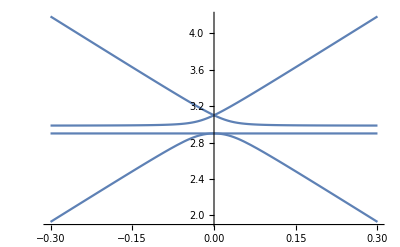

```mathematica
ω:=1
ϵ:=0.9
g:=0.1
Plot[Eigenvalues[H[ω,ϵ,V,g,3]],{V,-0.3,0.3}]
```

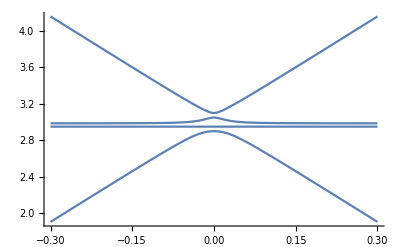

```mathematica
ω:=1
ϵ:=0.9
g:=0.05
Plot[Eigenvalues[H[ω,ϵ,V,g,3]],{V,-0.3,0.3}]
```

Single-excitation case

```mathematica
bTb0:=DiagonalMatrix[{1,0,0}]
Sz0:=DiagonalMatrix[{-1,0,0}]
DipDip0:=Normal[SparseArray[{{2,3}->1,{3,2}->1},{3,3}]]
DipF0:={{0,1,1},{1,0,0},
{1,0,0}}
H[ω_,ϵ_,V_,g_,0]:=ω bTb0+ϵ Sz0+V DipF0+g DipDip0
```

```mathematica
Det[H[ω, ϵ, V, g, 0]+DiagonalMatrix[{E,E,E}]]
```

ⅇ^3-ⅇ g^2-2 ⅇ V^2+2 g V^2-ⅇ^2 ϵ+g^2 ϵ+ⅇ^2 ω-g^2 ω

```mathematica
Eigenvalues[H[ω,ϵ,V,g,0]]
```

{-g,1/2 (g-ϵ+ω-√(g^2+8 V^2+2 g ϵ+ϵ^2-2 g ω-2 ϵ ω+ω^2)),1/2 (g-ϵ+ω+√(g^2+8 V^2+2 g ϵ+ϵ^2-2 g ω-2 ϵ ω+ω^2))}

```mathematica
Eigenvectors[H[ω,ϵ,V,g,0]]
```

{{0,-1,1},{-(g+ϵ-ω+√(g^2+8 V^2+2 g ϵ+ϵ^2-2 g ω-2 ϵ ω+ω^2))/(2 V),1,1},{-(g+ϵ-ω-√(g^2+8 V^2+2 g ϵ+ϵ^2-2 g ω-2 ϵ ω+ω^2))/(2 V),1,1}}

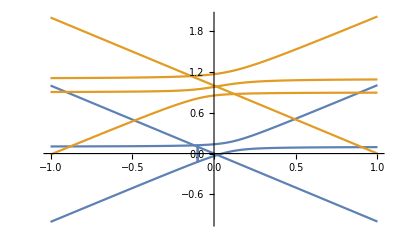

```mathematica
ω:=1
ϵ:=0.9
V:=0.05
Plot[{Eigenvalues[H[ω,ϵ,V,g,0]],Eigenvalues[H[ω,ϵ,V,g,1]]},{g,-1,1}]
```

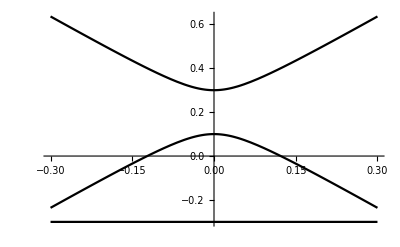

```mathematica
ω:=1
ϵ:=0.9
g:=0.1
Plot[Eigenvalues[H[ω,ϵ,V,g,0]],{V,-0.3,0.3}]
```

```mathematica
ω:=1
ϵ:=0.9
g:=0.3
Plot[Eigenvalues[H[ω,ϵ,V,g,0]],{V,-0.3,0.3}]
```

-Graphics-

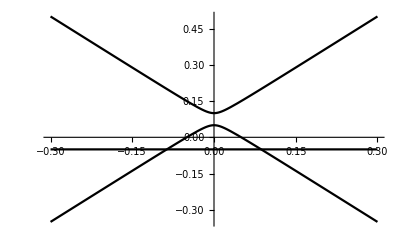

```mathematica
ω:=1
ϵ:=0.9
g:=0.05
Plot[Eigenvalues[H[ω,ϵ,V,g,0]],{V,-0.3,0.3}]
```

Well, of course the V-plots look like this...

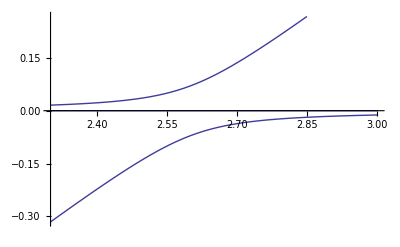

```mathematica
V=0.05;g=-0.0;ϵ=2.6;
Plot[Sort[Eigenvalues[H[ω,ϵ,V,g,0]]],{ω,2.3,3}]
```

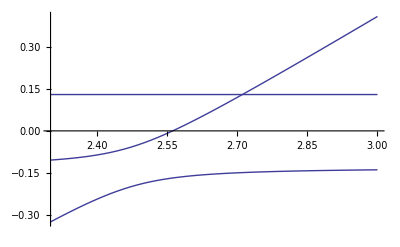

-gi^2 l+l^3+2 gi Vi^2-2 l Vi^2+gi^2 ϵi-l^2 ϵi-gi^2 ωi+l^2 ωi

```mathematica
V = 0.05; g = -0.13; ϵ = 2.6;
Plot[Sort[Eigenvalues[H[ω, ϵ, V, g, 0]]], {ω, 2.3, 3}]
```